```mathematica
Needs["DorisAlgorithmCompactCase`"]
```

(-3+x) (-2+x) (-1+x)^3 (3+x)

True

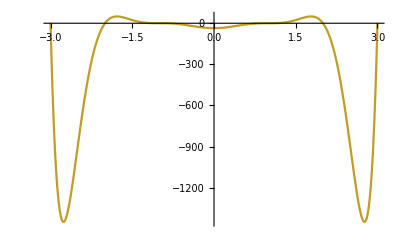

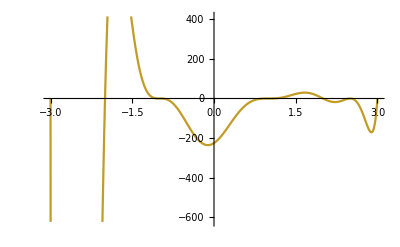

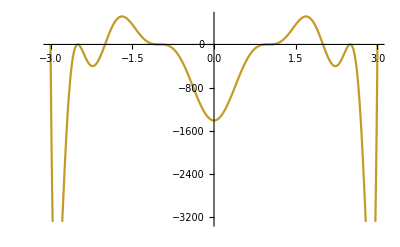

```mathematica
infix=(x+2)(x+1)^3;
outfix=(x+3)(x-1)^3(x-2)(x-3)
g=-outfix infix;
templateS1=a^2((x-b)^2+c^2);
DorisAlgorithmCompactCase[x,infix,{g}]
Plot[-g,{x,-3,3}]
Plot[-g (x-(2+3)/2)^2,{x,-3,3}]
Plot[-g (x-(2+3)/2)^2(x-(-2-3)/2)^2,{x,-3,3}]
```

```mathematica
Series[1+templateS1 outfix,{x,-2,10}]
Series[1+templateS1 outfix,{x,-1,10}]
```

(1-540 a^2 ((-2-b)^2+c^2))+27 a^2 (116+76 b+9 b^2+9 c^2) (x+2)+9 a^2 (-20+94 b+37 b^2+37 c^2) (x+2)^2+a^2 (243+333 (-4-2 b)-322 ((-2-b)^2+c^2)) (x+2)^3+a^2 (333-322 (-4-2 b)+110 ((-2-b)^2+c^2)) (x+2)^4+a^2 (-322+110 (-4-2 b)-17 ((-2-b)^2+c^2)) (x+2)^5+a^2 (110-17 (-4-2 b)+(-2-b)^2+c^2) (x+2)^6+a^2 (-21-2 b) (x+2)^7+a^2 (x+2)^8+O[x+2]^11

(1-192 a^2 ((-1-b)^2+c^2))+16 a^2 (43+62 b+19 b^2+19 c^2) (x+1)-32 (a^2 (29+27 b+4 b^2+4 c^2)) (x+1)^2+a^2 (304-128 (-2-2 b)-32 ((-1-b)^2+c^2)) (x+1)^3+a^2 (-128-32 (-2-2 b)+40 ((-1-b)^2+c^2)) (x+1)^4+a^2 (-32+40 (-2-2 b)-11 ((-1-b)^2+c^2)) (x+1)^5+a^2 (40-11 (-2-2 b)+(-1-b)^2+c^2) (x+1)^6+a^2 (-13-2 b) (x+1)^7+a^2 (x+1)^8+O[x+1]^11

```mathematica
sol=FindInstance[(1-540 a^2 ((-2-b)^2+c^2))==0&&27 a^2 (116+76 b+9 b^2+9 c^2) <0&&(1-192 a^2 ((-1-b)^2+c^2))==0&&16 a^2 (43+62 b+19 b^2+19 c^2)>0&&-3≤b≤-2,{a,b,c},Reals][[1]]
```

{a→-(√(29/510))/6,b→-41/16,c→(√(6355/29))/16}

```mathematica
s1=templateS1/.sol
Reduce[s1<0,x]
s0=infix(1+s1 outfix);
Reduce[s0<0,x]
s0+s1 g//Simplify
```

(29 (6355/7424+(41/16+x)^2))/18360

False

False

(1+x)^3 (2+x)

```mathematica
sol//N
```

{a→-0.0349362,b→-2.875,c→0.866958}

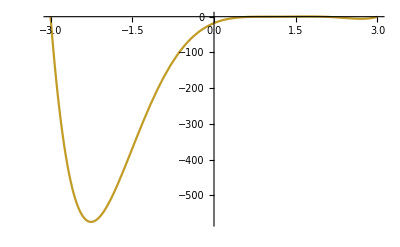

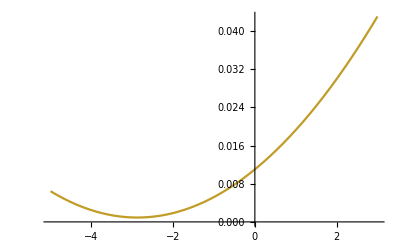

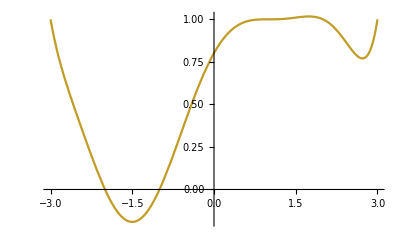

```mathematica
Plot[outfix,{x,-3,3}]
Plot[s1,{x,-5,3}]
Plot[(1+s1 outfix),{x,-3,3}]
```

```mathematica
{a->Root"-0.0291"Root[841-1054080 #1^2+74649600 #1^4&,2]-0.0291356353575097,b->-209/58+4320/29 (Root"-0.0291"Root[841-1054080 #1^2+74649600 #1^4&,2]-0.0291356353575097)^2,c->0}//N
```

{a→-0.0291356,b→-3.47699,c→0.}

```mathematica
Series[(1+s1 outfix),{x,-2,10}]
Series[(1+s1 outfix),{x,-1,10}]
```

-(693 (x+2))/1360+(3191 (x+2)^2)/16320+(11141 (x+2)^3)/29376+(11567 (x+2)^4)/73440-(25309 (x+2)^5)/73440+(4271 (x+2)^6)/29376-(3683 (x+2)^7)/146880+(29 (x+2)^8)/18360+O[x+2]^11

(389 (x+1))/612+(4871 (x+1)^2)/9180-(487 (x+1)^3)/1530-(929 (x+1)^4)/6120+(4387 (x+1)^5)/48960+(23 (x+1)^6)/1632-(203 (x+1)^7)/16320+(29 (x+1)^8)/18360+O[x+1]^11